```mathematica
SetDirectory[NotebookDirectory[]];
```

Disable current notebook FileOutlineCache and CellChangeTimes.  See: https://stackoverflow.com/questions/2816628/version-control-of-mathematica-notebooks

# Library

```mathematica
<<"mma-lib/groups.m";<<"mma-lib/xml.m";Needs["ErrorBarPlots`"]
```

```mathematica
<<"mma-lib/lattice.m";<<"mma-lib/linear-algebra.m";
```

## Lattice Saddle Point

```mathematica
<<"mma-lib/minres1.m";<<"mma-lib/minresqlp0.m";<<"mma-lib/minres.m";
```

```mathematica
methodName[x_]:=If[Head[x]===List,First[x],x];(* Tricky:  explicit Sequence[...] will disappear! *)
methodOptions[x_]:=Apply[Sequence,If[Head[x]===List,Rest[x],{}]];
```

Shift cutoff

```mathematica
applyCutoff1::usage="Rescale shifts for a single link.  Large zzz removes the cutoff.  When Norm[shift]=Pi, there is an inflection point in the associated color matrix meaning that the quadratic approximation becomes qualitatively different than the full matrix exponential.  Thus, we set shift to zero when Norm[shift]>=Pi.  The cutoff represents the Norm[shift] where the quadratic approximation *starts* breaking down.  In that case, we scale back the size of the shift.";applyCutoff1[hess_?VectorQ,grad_,cutoff_:1,zzz_:1]:=
Block[ (* First, see if any component exceeds the cutoff.  Thus, we avoid any divide-by-zero error. *){tooBig=Inner[(Pi zzz Abs[#1]≤Abs[#2])&,hess,grad,Or],shift},
If[tooBig,Map[0&,grad],
(* Otherwise, rescale based on the norm of the shift *)
shift=grad/hess;Which[Pi zzz<=Norm[shift],Map[0&,shift],Norm[shift]<cutoff  zzz, shift,True,(cutoff/Norm[shift]) shift ]]];shiftNorm[shifts_]:=Max[Map[Norm,Partition[shifts,nc^2-1]]];
applyCutoff2::usage="Rescale shifts on an entire lattice so that the largest norm of a shift on a link is less than the cutoff.";applyCutoff2[shifts_?ArrayQ,cutoff_:1,zzz_:1]:=Block[{maxNorm=shiftNorm[shifts]},If[maxNorm<cutoff zzz,shifts,Print["applyCutoff2: rescale maxNorm ",maxNorm," to ",cutoff];(cutoff/maxNorm) shifts]];applyCutoff3::usage="Apply cutoff to the eigenspace of the Hessian.  In this case, the shifts are independent, but have no direct meaning. We infer the effect on the lattice links by using the rotation back onto the lattice.  We demand that the norm of the largest shift on any single link be less than the cutoff (default value Pi)."; applyCutoff3[hess_,grad_,proj_,cutoff_:Pi,zzz_:1]:=Block[{maxLinkShift=Map[shiftNorm,proj],result,count=0,doPairs=False},If[doPairs,goodPairs0={};badPairs0={}];result=MapThread[If[cutoff zzz Abs[#1]≤Abs[#2] #3,count+=1;If[doPairs,AppendTo[badPairs0,{#1,#2}]];0,If[doPairs,AppendTo[goodPairs0,{#1,#2}]];#2/#1]&,{hess,grad,maxLinkShift}];If[count>0 ,Print["applyCutoff3:  ",count," of ",Length[hess], " zeros"]];result];
cutoffNullspace::usage="Select vectors in proj that are associated with shifts that violate the cutoff.";
cutoffNullspace[hess_,grad_,proj_,cutoff_:Pi,zzz_:1]:=Block[{result,count=0},result=MapThread[If[zzz<Infinity && cutoff zzz Abs[#1]≤Abs[#2] shiftNorm[#3],count+=1;#3,Nothing]&,{hess,grad,proj}];If[count>0 ||True ,Print["cutoffNullSpace:  ",count," of ",Length[hess], " zeros"]];result];
```

Define basis for describing lattice-wide shifts.   The parameter fixed describes the type of shift:
fixed == -1:  All possible shifts, including those associated with gauge transformations.
fixed == 0:  Shifts on a smaller basis where all shifts associated with gauge transformations have been removed.
fixed > 0:  For each Polyakov loop in the direction = fixed, apply a constant shift.

```mathematica
nGrad::usage="Size of basis for lattice-wide shifts.";nGrad[fixed_]:=If[fixed<1,nd,nd-1+1/latticeDimensions[[fixed]]]latticeVolume[]*(nc^2-1);coords2grad::usage="Use latticeIndex, rather than linearSiteIndex to order the sites, so we can handle fixed>0.";coords2grad[fixed_][dir_,coordsIn_,generator_]:=generator+(nc^2-1)*Block[{coords=coordsIn,dimensions=latticeDimensions},If[fixed==dir,coords[[fixed]]=1;dimensions[[fixed]]=1];latticeIndex[coords,dimensions]-1+ latticeVolume[]*Sum[If[fixed==k,1/latticeDimensions[[k]],1],{k,dir-1}]];nGauge::usage="Size of basis for a gauge tranformation.  fixed=0: arbitrary gauge tranformation.  fixed>0:  gauge transforms that preserve Axial gauge in the \"fixed\" direction.";
nGauge[fixed_]:=latticeVolume[](nc^2-1)If[fixed<1,1,1/latticeDimensions[[fixed]]];
coords2gauge[fixed_][coordsIn_,generator_]:=generator+(nc^2-1)*Block[{coords=coordsIn,dimensions=latticeDimensions},If[fixed>0,coords[[fixed]]=1;dimensions[[fixed]]=1];latticeIndex[coords,dimensions]-1];
gradLinkTake[fixed_][dir_,coords_]:={1,nc^2-1}+coords2grad[fixed][dir,coords,0];symAdd::index="Invalid index.";
SetAttributes[symAdd,HoldFirst];symAdd[m_,i_,j_,value_]:=(m[{i,j}]=Lookup[m,Key[{i,j}],0.0]+value;m[{j,i}]=Lookup[m,Key[{j,i}],0.]+value);SetAttributes[oneAdd,HoldFirst];oneAdd[m_,i_,j_,value_]:=m[{i,j}]=Lookup[m,Key[{i,j}],0.0]+value;reTrDot::usage="Compute Re[Tr[a.b]] where a and b are color matrices.";reTrDot=Compile[{{x,_Complex,2},{y,_Complex,2}},
Sum[Re[x[[i,j]] y[[j,i]]],{i,nc},{j,nc}],{{nc,_Integer}}];
```

```mathematica
gaugeTransformShifts::usage="Return a matrix containing shifts associated with all possible infinitesimal gauge transformations.  The result is returned as a SparseArray.";
gaugeTransformShifts::axial="Not Axial gauge.";SetAttributes[gaugeTransformShifts,HoldFirst];gaugeTransformShifts[rootGaugeField_,fixed_:-1]:=ParallelSum[Block[{gaugeShifts=Association[],gen=suGenerators[],c2grad=coords2grad[fixed]},Do[Block[{coords=latticeCoordinates[i],gindex,index1,index2,u1,u2,ugu1,ugu2},u1=getLink[rootGaugeField][dir,coords];u2=getLink[rootGaugeField][dir,shift[dir,coords,-1]];(* Only do the axial direction once. But verify that lattice is in Axial gauge. *)
If[dir==fixed && coords[[fixed]]>1,If[AnyTrue[Abs[u1-u2],#>10^-6&,2],Message[gaugeTransformShifts::axial];Return[$Failed]];Continue[]];
gindex=coords2gauge[fixed][coords,gac];
index1=c2grad[dir,coords,0];
ugu1=ConjugateTranspose[u1].gen[[gac]].u1;index2=c2grad[dir,shift[dir,coords,-1],0];ugu2= u2.gen[[gac]].ConjugateTranspose[u2];Do[oneAdd[gaugeShifts,gindex,index1+ac,2 reTrDot[ugu1,gen[[ac]]]];oneAdd[gaugeShifts,gindex,index2+ac,-2 reTrDot[ugu2,gen[[ac]]]],{ac,nc^2-1}]],{i,kernel,latticeVolume[],$KernelCount},{gac,nc^2-1},{dir,nd}];SparseArray[Normal[gaugeShifts],{nGauge[fixed],nGrad[fixed]}]],{kernel,$KernelCount}];dynamicPart::usage="Dynamic (non gauge shift) part of a shift vector.  This returns a function that can be applied to any shift vector.";Options[dynamicPart]={Method->Automatic};dynamicPart[gaugeTransformShifts_,OptionsPattern[]]:=Module[{
(* Project out any gauge transform part of the vector. *)
(* These two give the same result, but the least-squares solver is about 4 times faster. *)
projection=Which[
(* Default dense method. *)
OptionValue[Method]===Automatic||OptionValue[Method]==="dense",LeastSquares[Transpose[gaugeTransformShifts],#]&,
(* Sparse method, using Krylov, possibly QMR? *)
methodName[OptionValue[Method]]==="QMR",(* Since the gauge fields were calculated in single precision, we choose a compatible default tolerance.  
This tends to be slow, since the matrix is poorly conditioned. Maybe use some kind of restart strategy? *)
LeastSquares[Transpose[gaugeTransformShifts],#,methodOptions[OptionValue[Method]],Method->"Krylov",Tolerance->10.0^-7]&,
(* In the sparse case, this should be numerically equivalent, but slower for ill-conditioned matrices. *)
(* This may be a faster dense method, since factorization is pre-computed? *)methodName[OptionValue[Method]]==="LinearSolve",Module[{linearSolve=LinearSolve[gaugeTransformShifts.Transpose[gaugeTransformShifts],methodOptions[OptionValue[Method]]]},linearSolve[gaugeTransformShifts.#]&]]},(#-projection[#].gaugeTransformShifts)&];
```

Whole lattice at once. 
fixedDir>0 applies the same shift to all links in each Polyakov loop winding around the lattice in direction fixedDir.  Thus, it is compatible with choosing an Axial gauge in that direction.  This should remove most gauge invariant shifts

```mathematica
Options[latticeHessian]={allLinks->True,fixedDir->-1};latticeHessian::usage="Set allLinks to False to compare with single-link code.  Option fixedDir>0 will apply a constant shift to any link a given Polyakov loop winding in that direction, compatible with choosing an Axial gauge in that direction.";latticeHessian[getRootLink_,OptionsPattern[]]:=Block[{fixed=OptionValue[fixedDir]},(* Adding elements to a SparseArray one at a time is very inefficient in Mathematica; see https://mathematica.stackexchange.com/questions/777/efficient-by-element-updates-to-sparsearrays.  Instead, we accumulate Array elements in an Association and create a SparseArray at the end. *)Block[{hess=Association[],grad=Array[0.0&,nGrad[fixed]],gen=suGenerators[]+0.0 I,sym=0.5*Outer[(#1.#2+#2.#1)&,suGenerators[],suGenerators[],1]+0.0 I,coords},innerLoopTime=0;Do[coords=latticeCoordinates[i];(* Number of color matrix multiplications:
(number of plaquettes) (16 + nc (16 + 10 nc)) 
*)
Block[{c00=ConjugateTranspose[getRootLink[dir2,coords]].getRootLink[dir1,coords],c10=getRootLink[dir1,coords].getRootLink[dir2,shift[dir1,coords]],c11=getRootLink[dir2,shift[dir1,coords]].ConjugateTranspose[getRootLink[dir1,shift[dir2,coords]]],c01=ConjugateTranspose[getRootLink[dir1,shift[dir2,coords]]].ConjugateTranspose[getRootLink[dir2,coords]],s1,s2,s3,s4,v00,v10,v11,v01,w1,w2,w3,w4},
s1=c00.c10;s2=c10.c11;s3=c11.c01;s4=c01.c00;v00=c01.s1 (* =s4.c10 *);
v10=c00.s2 (* =s1.c11 *);v11=c10.s3 (* =s2.c01 *);v01=c11.s4 (* =s3.c00 *);w1=s4.s2;w2=s1.s3;w3=s2.s4;w4=s3.s1;Do[Block[{g1=coords2grad[fixed][dir1,coords,ca1],g2=coords2grad[fixed][dir2,shift[dir1,coords],ca1],g3=coords2grad[fixed][dir1,shift[dir2,coords],ca1],g4=coords2grad[fixed][dir2,coords,ca1],
ss42=s4.gen[[ca1]].s2,ss13=s1.gen[[ca1]].s3,
vv0011=v00.gen[[ca1]].c11,vv1001=v10.gen[[ca1]].c01,vv1100=v11.gen[[ca1]].c00,vv0110=v01.gen[[ca1]].c10,t0,z},
(* Negative for inverse links. *)
grad[[g1]]+=-Im[Tr[w3.gen[[ca1]]]];grad[[g3]]+=Im[Tr[w1.gen[[ca1]]]];
grad[[g2]]+=-Im[Tr[w4.gen[[ca1]]]];grad[[g4]]+=Im[Tr[w2.gen[[ca1]]]];
(* Time is dominated by matrix construction, and matrix construction is dominated by the inner color loop. *)
t0=SessionTime[];Do[Block[{gg1=g1-ca1+ca2,gg2=g2-ca1+ca2,gg3=g3-ca1+ca2,gg4=g4-ca1+ca2},
oneAdd[hess,g1,gg1,-reTrDot[sym[[ca1,ca2]],w3]];
oneAdd[hess,g3,gg3,-reTrDot[sym[[ca1,ca2]],w1]];
oneAdd[hess,g2,gg2,-reTrDot[sym[[ca1,ca2]],w4]];
oneAdd[hess,g4,gg4,-reTrDot[sym[[ca1,ca2]],w2]];
If[OptionValue[allLinks],
symAdd[hess,g1,gg3,reTrDot[ss42,gen[[ca2]]]];symAdd[hess,g2,gg4,reTrDot[ss13,gen[[ca2]]]];
symAdd[hess,g2,gg3,reTrDot[vv0011,gen[[ca2]]]];symAdd[hess,g3,gg4,-reTrDot[vv1001,gen[[ca2]]]];symAdd[hess,g4,gg1,reTrDot[vv1100,gen[[ca2]]]];symAdd[hess,g1,gg2,-reTrDot[vv0110,gen[[ca2]]]]]],{ca2,nc^2-1}];innerLoopTime+=SessionTime[]-t0],{ca1,nc^2-1}]],{dir1,nd-1},{dir2,dir1+1,nd},{i,latticeVolume[]}];{SparseArray[Normal[hess]],grad}]];
```

```mathematica
findDelta::usage="Given a Hessian matrix and a gradient, find the associated shifts using either dense or sparse matrix techniques.";Options[findDelta]={dynamicPartMethod->Automatic,Method->Automatic,rescaleCutoff->1,dampingFactor->1,storePairs->False,largeShiftSearch->Automatic,
(* Roughly speaking, the relative error in the matrix norm of the link goes as Norm[shift]^3/48. *)
cutoffValue->2};(* Dense matrix version (default) *)findDelta[hessIn_,gradIn_,gaugeTransformShifts_,OptionsPattern[]]:=Block[{hess,grad,zzz=OptionValue[rescaleCutoff],cutoff=OptionValue[cutoffValue],damping=OptionValue[dampingFactor],values,oo,proj,shifts},
If[MatrixQ[gaugeTransformShifts],(* Find projection onto subspace orthogonal to all gauge transforms.  proj is dense. *)
proj=NullSpace[gaugeTransformShifts];hess=proj.hessIn.Transpose[proj];grad=proj.gradIn,
(* Normal case: no projection onto the subspace. *)proj=IdentityMatrix[Length[hessIn],SparseArray];hess=hessIn;grad=gradIn];{values,oo}=Eigensystem[Normal[hess]];shifts=applyCutoff3[values,oo.grad,oo.proj,2,zzz].oo.proj;Print["shifts norms and rescale:  ",{shiftNorm[shifts],Norm[shifts],shifts.hessIn.shifts/shifts.gradIn}];If[OptionValue[storePairs],hess0=hess;grad0=grad;oo0=oo;pairs0=Transpose[{values,oo.grad}];proj0=proj;shifts0=shifts];-damping applyCutoff2[shifts,cutoff,zzz]]/;OptionValue[Method]===Automatic||OptionValue[Method]==="Dense";

(* MINRES/MINRES-QLP version
To remove large shift eigenvalues, switch over to a dense calculation.  This is correct, but may take up too many resources for a large calculation.  Perhaps, one can do this within the MINRES code itself, having the Lanczos method switch over to finding eigenvalues and eigenvectors. *)minresLabels=Association["MINRES"->minres,"MINRES1"->minres1,"MINRES-QLP"->minresqlp0,"MINRES-QLP0"->minresqlp0];findDelta[hess_,grad_,gaugeTransformShifts_,opts:OptionsPattern[]]:=Module[{recordW={},snl=None,snll=None,sn},Block[{zzz=OptionValue[rescaleCutoff],minresFun=minresLabels[methodName[OptionValue[Method]]],cutoff=OptionValue[cutoffValue],damping=OptionValue[dampingFactor],result,shifts,recordStep=Function[{iter,x,w,v},sn=shiftNorm[x];If[Pi Abs[w.hess.w]<=Abs[w.grad]shiftNorm[v],AppendTo[recordW,w];Print[iter,":  record W ",Length[recordW]]];If[snl===None||snll===None||Sign[sn-snl]*Sign[snl-snll]<0,Print[iter,":  Norms:  ",{sn,Norm[x]}]];snll=snl;snl=sn],
dp=If[MatrixQ[gaugeTransformShifts],dynamicPart[gaugeTransformShifts,Method->OptionValue[dynamicPartMethod]],Identity],smallProj},
(* Calculate eigenvectors associated with shifts that are too large.  Since, the Mma routine Eigensystem[...] doesn't allow the matrix to be given as a function, we use ersatzLanczos[] as a work-around. *)smallProj=Block[{vals,vecs,nsmall=If[OptionValue[largeShiftSearch]=!=Automatic,OptionValue[largeShiftSearch],
(* This estimate is ad-hoc.  Perhaps one could use the distribution of pairs? *)
Floor[Length[grad]/10]]},{vals,vecs}=ersatzLanczos[dp[hess.#]&,Length[grad],eigenPairs->-nsmall,initialVector->grad,maxIterations->2 nsmall,printDetails->True];Module[{largeShiftSpace=cutoffNullspace[vals,vecs.grad,vecs,2,OptionValue[rescaleCutoff]]},If[Length[largeShiftSpace]>0,(#-(largeShiftSpace.#).largeShiftSpace)&,Identity]]];(* Call the appropriate MINRES routine, setting some default values. *)result=minresFun[dp[smallProj[hess.#]]&,dp[smallProj[grad]],methodOptions[OptionValue[Method]],Apply[Sequence,FilterRules[{stepMonitor->recordStep,localSize->5000,subspaceProjector->(Block[{y=dp[smallProj[#]]},If[False,Print["    reortho overlap:  ",#.y/#.#]];y]&)},Options[minresFun]]]];shifts=result[[1]];
(* Verify result is in the subspace *)Print["Result overlap with small shift subspace, dynamicPart, and both:  ",{shifts.smallProj[shifts],shifts.dp[shifts],shifts.dp[smallProj[shifts]]}/shifts.shifts];
shifts=dp[smallProj[shifts]];
Block[{rescale=Abs[shifts.grad]/Abs[shifts.hess.shifts]},Print["rescale factor: ",rescale];shifts*=rescale];
Print["shiftNorm is now: ",shiftNorm[shifts]];
If[False&&Length[recordW]>0,
(* Similar to the dense matrix calculation, determine the eigenvalues that have shifts that are too large, using the
subspace defined by W.  *)
Block[{proj=Orthogonalize[recordW],hvals,oo,ns},{hvals,oo}=Eigensystem[proj.hess.Transpose[proj]];ns=cutoffNullspace[hvals,oo.proj.grad,oo.proj,Pi,zzz];
Print["Overlap of shifts with nullSpace:  ",1-Norm[ns.shifts]^2/shifts.shifts];
(* Assume that ns is othronormal, project out the large shifts. *)If[ Length[ns]>0,shifts=shifts-Transpose[ns].ns.shifts]]];
If[OptionValue[storePairs],hess0=hess;grad0=grad;oo0=None;pairs0=None;proj0=None;shifts0=shifts];-damping applyCutoff2[shifts,cutoff,zzz]]]/;KeyExistsQ[minresLabels,methodName[OptionValue[Method]]];
```

```mathematica
SetAttributes[applyDelta,HoldFirst];
applyDelta[tgf_,delta_,fixed_]:=Block[{gradMap=gradLinkTake[fixed]},Do[Block[{coords=latticeCoordinates[i]},tgf[[dir,linearSiteIndex[coords]]]=getLink[tgf][dir,coords].MatrixExp[I Take[delta,gradMap[dir,coords]]. suGenerators[]].getLink[tgf][dir,coords]],{dir,nd},{i,latticeVolume[]}]];
```

```mathematica
latticeSaddlePointStep::usage="Setting the option fixedDir=0 will use a projection onto the subspace orthogonal to all gauge transforms.  This should be the most correct method.  Can apply this to both dense and sparse systems.";
(* For passing options through to subfunctions:  
https://mathematica.stackexchange.com/questions/353/functions-with-options/ *)
Options[latticeSaddlePointStep]=Join[Options[findDelta],Options[latticeHessian]];latticeSaddlePointStep[opts:OptionsPattern[]]:=Block[{hess,grad,delta,tmpGaugeField=makeRootLattice[],t0=SessionTime[],t1,t2,t3},{hess,grad}=latticeHessian[getLink[tmpGaugeField],Apply[Sequence,FilterRules[{opts},Options[latticeHessian]]]];t1=SessionTime[];(* Debug prints *)
Which[False,
Print["hessian difference:  ",Chop[Normal[hess]-hess0]];
Print["gradient difference:  ",Chop[grad-gradient0]],
False,
Print["hessian:",Normal[hess]];
Print["gradient:  ",grad],
False,
Print["hessian, first link:  ",Normal[Take[hess,nc^2-1,nc^2-1]]];
Print["gradient, first link:  ",Take[grad,nc^2-1]]];
delta=findDelta[hess,grad,If[OptionValue[fixedDir]>-1,gaugeTransformShifts[tmpGaugeField,OptionValue[fixedDir]],None],Apply[Sequence,FilterRules[{opts},Options[findDelta]]]];(* Debug prints *)
Which[False,Print["delta difference:  ",Chop[delta-delta0]],False,
Print["delta:  ",delta],False,
Print["delta, first link:  ",Take[delta,nc^2-1]]];
t2=SessionTime[];applyDelta[tmpGaugeField,delta,OptionValue[fixedDir]];t3=SessionTime[];Print["times:  ",{innerLoopTime,t1-t0,t2-t1,t3-t2}];tmpGaugeField]
```

### One link shifts

Do a link at a time.  This is mostly for posterity & debugging since the resulting action density was dominated by one-plaquette spikes.

```mathematica
linkSaddlePointStep::usage="One iteration of the saddle point search.  Set rescaleCutoff to a large number to test this against the explicit calculation.";Options[linkSaddlePointStep]={rescaleCutoff->1,dampingFactor->1,printHessian->False,printShift->False,makeHess0->False};linkSaddlePointStep[u2Staples_,u1_,OptionsPattern[]]:= Block[{zzz=OptionValue[rescaleCutoff],cutoff=Min[0.1,If[NumberQ[beta],Sqrt[nc^2/(3 beta)],1]],damping=OptionValue[dampingFactor],debug=False,ff=u2Staples.u1,grad,mm,oo,values,deltas,sqrtU,nc=Length[u2Staples]},If[False,Print["cutoff:  ",cutoff]];grad=Map[Tr[ff.#]&,suGenerators[]];
If[debug,Print["grad:  ",grad]];(* Solve linear system mm.shifts = -Im[grad], paying careful attention to nullspace of mm.  Could equivalently use LDL^T factorization with symmetric pivoting.  *)mm=Re[Tr[ff]]/(2.0 Length[ff]) IdentityMatrix[Length[grad]]+suSymmetric[].Re[grad]/2.0;{values,oo}=Eigensystem[mm];
(* Using the fact that the periodicity of B_a is 4 Pi or less. *) deltas=-damping applyCutoff1[values,oo.Im[grad],cutoff,zzz];
If[OptionValue[printHessian],Print["Hessian:  ",mm];Print["gradient:  ",Im[grad]]];If[OptionValue[printShift],Print["shifts:  ",deltas.oo]];If[OptionValue[makeHess0],gradient0=Join[gradient0,-Im[grad]];hess0=If[MatrixQ[hess0],ArrayFlatten[{{hess0,0},{0,-mm}}],-mm];delta0=Join[delta0,deltas.oo]];{u1.MatrixExp[I deltas.oo.suGenerators[]],Max[Abs[deltas]]}];linkSaddlePoint::usage="Saddle point search for a single link.";
Options[linkSaddlePoint]=Join[{tolerance->10^-6,maxCount->1,printHessian->False,printShift->False,printDebug->False,updateGaugeField->True},Options[linkSaddlePointStep]];
linkSaddlePoint[dir_,coords_,opts:OptionsPattern[]]:= 
Block[{maxShift=4 Pi,u1=SUPower[getLink[dir,coords],0.5],u2,u2SumStaples,count=0,uu},u2=u1;
u2SumStaples=u2.sumStaples[dir,coords];
While[maxShift>OptionValue[tolerance]&&count<OptionValue[maxCount],count++;
{u1,maxShift}=linkSaddlePointStep[u2SumStaples,u1,Apply[Sequence,FilterRules[{opts},Options[linkSaddlePointStep]]]];If[OptionValue[printDebug],Print["Max shift:  ",maxShift]]];uu=u1.u2;
If[OptionValue[printDebug],SUMatrixQ[uu]];
If[OptionValue[updateGaugeField],setLink[dir,coords,uu]];{uu,maxShift}];Options[latticeSaddlePoint]=Join[{maxCount->1,tolerance->10^-6},Options[linkSaddlePoint]];latticeSaddlePoint[opt:OptionsPattern[]]:=Block[{count=0,maxShift=4 Pi,linkShift,stats={},stat,uu,newGaugeField},While[count<OptionValue[maxCount]&&maxShift>OptionValue[tolerance],maxShift=0;If[OptionValue[makeHess0],gradient0={};hess0=Null;delta0={}];newGaugeField=Table[{uu,linkShift}=linkSaddlePoint[dir,latticeCoordinates[k], maxCount->1,Apply[Sequence,FilterRules[{opt},Options[linkSaddlePoint]]]];maxShift=Max[linkShift,maxShift];uu,{dir,nd},{k,latticeVolume[]}];Print[stat={count, maxShift,averagePlaquette[]}];If[False,AppendTo[stat,exponentialModel[talliesToAverageErrors[polyakovLoopTallies["simple"]],printResult->True]]];AppendTo[stats,stat];count++];{newGaugeField,stats}];
```

# Testing

## Parallel processors

For parallelization, I had to go to menu Evaluation->Parallel Kernel Configuration and set the number manually.  Automatic launching of additional kernels is broken?  Note that the parallelization is based on the leading dimension of the table.
Verify parallel kernels are running:

```mathematica
ParallelEvaluate[$ProcessID]
```

{25215,25218,25237,25273,25322,25379}

## matrixPower, SU(N) generators

```mathematica
x=centerSUMatrix[1,7]
```

{{ⅇ^((2 ⅈ π)/7),0,0,0,0,0,0},{0,ⅇ^((2 ⅈ π)/7),0,0,0,0,0},{0,0,ⅇ^((2 ⅈ π)/7),0,0,0,0},{0,0,0,ⅇ^((2 ⅈ π)/7),0,0,0},{0,0,0,0,ⅇ^((2 ⅈ π)/7),0,0},{0,0,0,0,0,ⅇ^((2 ⅈ π)/7),0},{0,0,0,0,0,0,ⅇ^((2 ⅈ π)/7)}}

```mathematica
x=randomSUMatrix[7];
```

```mathematica
x=gaugeField[[3,15]]
```

{{0.956699+0.0406712 ⅈ,-0.0499901-0.0667599 ⅈ,0.130659+0.242991 ⅈ},{0.00153986-0.0254554 ⅈ,-0.476965-0.828118 ⅈ,-0.184021-0.228496 ⅈ},{-0.14496-0.247807 ⅈ,0.173146-0.223135 ⅈ,-0.420856+0.812828 ⅈ}}

```mathematica
SUMatrixQ[x]
```

True

Take the root

```mathematica
z=SUPower[x,0.2];
```

```mathematica
SUMatrixQ[z]
```

True

```mathematica
Norm[z.z.z.z.z-SUPower[x,1],Infinity]
```

2.32624×10^-15

```mathematica
matrixEqual[z.z.z.z.z,x]
```

True

Test normalization & orthogonality of the SU (N) generators

```mathematica
TableForm[Block[{x=suGenerators[4]},Table[Tr[x[[i]].x[[j]]],{i,Length[x]},{j,Length[x]}]]]
```

## Compare Mathematica mean plaquette against chroma value

Compare with chroma output xml file.

These should match plane_ij_plaq.

```mathematica
InputForm[Table[If[dir1<dir2,Mean[Table[plaquette[dir1,dir2,latticeCoordinates[i]]/nc,{i,latticeVolume[]}]]],{dir1,2},{dir2,dir1+1,3}]]
```

{{0.9424840512244733, 0.9432405719201301}, {0.9357560701712518}}

This should match w_plaq

```mathematica
InputForm[Mean[Flatten[%]]]
```

0.9404935644386184

## Compare the mean plaquette against Teper’s results

"w_plaq" is average of all plaquettes.

```mathematica
expr=Import["../data/3-4/periodic-16-28-out.xml"];
```

```mathematica
expr=Import["../data/3-4/periodic-16-33-out.xml"];
```

```mathematica
expr=Import["../data/3-3/periodic-24-21-out.xml"];
```

Pull out the average plaquette from the production lattice updates.

```mathematica
Length[wp=Flatten[xmlFilter[expr[[2]],{"purgaug","doHB","MCUpdates","elem","Update","InlineObservables","elem","Plaquette","w_plaq"}]]]
```

80000

Mean and standard error, ignoring autocorrelations.  
For SU(4), 2+1 dimensions, L=16^3 lattice, beta=28 abd 33, the average plaquette values match Teper’s result.  See arXiv:hep-lat/0206027v1 24 Jun 2002.

```mathematica
{Mean[wp],StandardDeviation[wp]/Sqrt[Length[wp]]}
```

{0.867669,1.4056×10^-6}

What is the effect of autocorrelations on the error estimate?  Using https://en.wikipedia.org/wiki/Unbiased_estimation_of_standard_deviation
Find a model for the autocorrelation function (ACF), fitting to an exponential:

```mathematica
data=Block[{cutoff=20},Transpose[{Table[k,{k,0,cutoff}],Log[CorrelationFunction[wp,{cutoff}]]}]];
```

```mathematica
ff=Fit[Take[data,5],{x},x]
```

-0.287291 x

```mathematica
Show[ListPlot[data,PlotRange->All],Plot[ff,{x,0,20}]]
```

From the Wikipedia article, the correction to the standard error is Sqrt[gamma2/gamma1], where :

```mathematica
gamma1[n_]:=1-2/(n-1) Sum[(1-x/n) Exp[ff],{x,1,n-1}]
```

```mathematica
gamma2[n_]:=1+2 Sum[(1-x/n) Exp[ff],{x,1,n-1}]
```

Since n is large, look at leading order in n :

```mathematica
{gamma1[Infinity],gamma2[Infinity]}
```

{1.,7.00941}

```mathematica
2/(1-Exp[ff])-1/.x->1
```

7.00941

There is a modest impact on the standard error, with the error estimate now matching Teper’s error estimate.  Good agreement for both SU(3) and SU(4).

```mathematica
{Mean[wp],StandardDeviation[wp] Sqrt[gamma2[Infinity]/Length[wp]]}
```

{0.867669,3.72138×10^-6}

## Polyakov loop, string tension

Test with trivial lattice.

```mathematica
nc=3;nd=3;latticeDimensions={4,6,8};makeTrivialLattice[]
```

Lattice with constant link in one direction.  Smeared Polyakov loop should give the same result as the simple Polyakov loop.

```mathematica
gaugeField=Block[{uu=randomSUMatrix[]},Print["Trace:  ",Tr[uu]];uu=SUPower[uu,1/latticeDimensions[[1]]];Table[If[dir==1,uu,IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}]];
```

Trace:  -0.99315-1.85067 ⅈ

```mathematica
polyakovLoop[1,{1,1,3}]
```

-0.99315-1.85067 ⅈ

```mathematica
polyakovLoop[1,{1,1,3},{2},{1}]
```

-0.99315-1.85067 ⅈ

```mathematica
loopThickness[]
```

11.6976

```mathematica
tallyData=talliesToAverageErrors[polyakovLoopTallies["simple"]]
```

```mathematica
tallyData=talliesToAverageErrors[polyakovLoopTallies["smeared"]]
```

<|1→{0.0041704,0.00030151},2→{0.00347826,0.00032425},3→{0.00245383,0.000282537},4→{0.00177564,0.000268184},5→{0.00127559,0.00027108},6→{0.000828947,0.000257286},7→{0.000470771,0.000271489},8→{-0.0000630903,0.000274988},9→{-0.000487348,0.000287281},10→{-0.000641494,0.000289092},11→{-0.000761984,0.00037373},√221→{-0.00114558,0.000372614}|>

```mathematica
ff=exponentialModel[tallyData,printResult->True];
```

| Estimate | Standard Error | t-Statistic | P-Value
norm | 0.00656738 | 0.000542036 | 12.1161 | 2.66832×10^-7
aw | 0.365636 | 0.0334032 | 10.9461 | 6.90016×10^-7

```mathematica
Block[{nn=Normal[tallyData],maxx,miny,maxy},maxx=Max[Map[First,nn]]+0.5;maxy=Max[Map[#[[2,1]]+1.5 #[[2,2]]&,nn]];miny=Min[0,Min[Map[#[[2,1]]-1.5 #[[2,2]]&,nn]]];Show[ErrorListPlot[Map[{{#[[1]],#[[2,1]]},ErrorBar[#[[2,2]]]}&,nn],PlotRange->{{0,maxx},{miny,maxy}},Epilog->{Text[ColumnForm[Join[Map[Row[{#[[1,1]]," = ",#[[1,2]],"±",#[[2]]}]&,Transpose[ff[{"BestFitParameters","ParameterErrors"}]]],{Row[{"β = ",N[beta],", N_d = ",nd,", N_c = ",nc}],Row[{"lattice = ",Row[latticeDimensions,", "]}]}]],{maxx*0.9,maxy*0.9},{1,1}],Dashing[.02],Gray,Line[{{0,0},{maxx,0}}]},Axes->False,Frame->True,FrameLabel->{"separation (links)","Polyakov loop correlator"}],Plot[ff[x],{x,0,maxx},PlotRange->All]]]
```

## Axial gauge

```mathematica
<<"test-4.m"
```

```mathematica
averagePlaquette[]
```

0.940494

```mathematica
setAxialGauge[3]
```

```mathematica
averagePlaquette[]
```

0.940494

## staples

```mathematica
<<"test-3-3-5.m"
```

```mathematica
xxx=averagePlaquette[]
```

0.940494

Set all links to the identity

```mathematica
gaugeField=Array[IdentityMatrix[nc]&,{nd,latticeVolume[]}];
```

```mathematica
sumStaples[1,{1,1,1}]
```

{{4,0,0},{0,4,0},{0,0,4}}

```mathematica
stapleTest[]
```

1

## nearest stationary point for single link and sum of staples

Test stationary point routine against an explicit calculation for a random staple and starting matrix.  To compare,  remove the damping factors in the function saddlePointStep[] by setting rescaleCutoff to a large number and dampingFactor to 1.

```mathematica
nd=3;nc=3;
```

```mathematica
makeRandomStaple[]:=Sum[randomSUMatrix[],{2 nd-2}];Clear[bb,bVector];bVector=Table[bb[i],{i,nc^2-1}].suGenerators[]
```

{{bb[3]/2,bb[1]/2-1/2 ⅈ bb[2]},{bb[1]/2+1/2 ⅈ bb[2],-bb[3]/2}}

### Run test

Make random staple and starting link.

```mathematica
testStaple=makeRandomStaple[];uu=randomSUMatrix[];sqrtU=SUPower[uu,0.5];
```

Explicitly find the second order expansion of the exponential.

```mathematica
expr=Re[Expand[Tr[testStaple.sqrtU.Simplify[IdentityMatrix[nc]+I bVector-bVector.bVector/2!].sqrtU]]]//.{Re[a_+b_]->Re[a]+Re[b],Re[a_ bb[i_]]->Re[a] bb[i],Re[a_ bb[i_]^n_]->Re[a] bb[i]^n}
```

-1.60303+0.220397 bb[1]+0.0152886 bb[1]^2-0.040771 bb[2]-0.0884741 bb[1] bb[2]+0.256089 bb[2]^2+0.112573 bb[3]-0.232988 bb[1] bb[3]-0.104331 bb[2] bb[3]+0.129379 bb[3]^2+0.537901 bb[4]-0.314012 bb[2] bb[4]-0.0935483 bb[3] bb[4]+0.0152886 bb[4]^2-0.5556 bb[5]+0.314012 bb[1] bb[5]-0.144072 bb[3] bb[5]-0.0884741 bb[4] bb[5]+0.256089 bb[5]^2-0.180506 bb[6]-0.0935483 bb[1] bb[6]+0.144072 bb[2] bb[6]+0.232988 bb[4] bb[6]-0.104331 bb[5] bb[6]+0.129379 bb[6]^2+0.80328 bb[7]-0.232988 bb[2] bb[7]+0.0884741 bb[3] bb[7]-0.0935483 bb[5] bb[7]-0.314012 bb[6] bb[7]+0.0152886 bb[7]^2+0.158609 bb[8]-0.120471 bb[1] bb[8]+0.134516 bb[2] bb[8]+0.0510805 bb[3] bb[8]-0.16636 bb[4] bb[8]+0.0540101 bb[5] bb[8]-0.181295 bb[6] bb[8]+0.146312 bb[7] bb[8]+0.251883 bb[8]^2

Find the stationary point, based on this :

```mathematica
sp=Solve[Table[D[expr,bb[i]]==0,{i,nc^2-1}],Table[bb[i],{i,nc^2-1}]][[1]]
```

{bb[1]→1.3623,bb[2]→1.83287,bb[3]→2.45122,bb[4]→0.989808,bb[5]→1.68051,bb[6]→1.27942,bb[7]→1.3935,bb[8]→-0.524618}

```mathematica
v1=sqrtU.MatrixExp[I bVector/.sp].sqrtU
```

{{-0.105001+0.747176 ⅈ,-0.376393+0.292519 ⅈ,-0.368804+0.259705 ⅈ},{-0.0258467-0.0870856 ⅈ,-0.688351-0.124348 ⅈ,0.643755+0.296713 ⅈ},{-0.615259-0.209539 ⅈ,0.32144+0.424439 ⅈ,0.129984+0.526481 ⅈ}}

```mathematica
centerPhases[v1]
```

{0.68794,2.0942,-2.78214}

Now, compare this with the library routine (with damping factors removed) :

```mathematica
{u2,maxShift}=linkSaddlePointStep[sqrtU.testStaple,sqrtU,rescaleCutoff->Infinity,dampingFactor->1]
```

{{{0.408915+0.250898 ⅈ,0.0378767+0.342768 ⅈ,-0.610661+0.527264 ⅈ},{-0.0202353+0.259688 ⅈ,-0.605232-0.61896 ⅈ,0.0720023+0.421368 ⅈ},{-0.837651+0.0182176 ⅈ,-0.0482895+0.359619 ⅈ,-0.00241311+0.407854 ⅈ}},3.18143}

```mathematica
v2=u2.sqrtU
```

{{-0.105001+0.747176 ⅈ,-0.376393+0.292519 ⅈ,-0.368804+0.259705 ⅈ},{-0.0258467-0.0870856 ⅈ,-0.688351-0.124348 ⅈ,0.643755+0.296713 ⅈ},{-0.615259-0.209539 ⅈ,0.32144+0.424439 ⅈ,0.129984+0.526481 ⅈ}}

```mathematica
centerPhases[v2]
```

{0.68794,2.0942,-2.78214}

## nearest stationary point for entire lattice

Test stationary point routine against an explicit calculation for a random lattice.  Tested for nd=3 and SU(2), SU(3) with multiple sites, and SU(4) with one site.

Create Random lattice :

```mathematica
nd=3;nc=2;latticeDimensions={2,2,1};gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];
(* Switch order to verify we are not dependent on latticeCoordinates[] indexing. *)Do[linearSiteIndex[latticeCoordinates[i]]=If[True,i,latticeVolume[]-i+1],{i,latticeVolume[]}];averagePlaquette[]
```

0.114169

```mathematica
Clear[bb,bVector];bVector[dir_,site_]:=(Table[bb[dir,site,i],{i,nc^2-1}].suGenerators[])
```

Create links with second order perturbation.  Variables have same lattice index as links.

```mathematica
uu=Table[Simplify[SUPower[gaugeField[[dir,i]],0.5].(IdentityMatrix[nc]+I bVector[dir,i]-bVector[dir,i].bVector[dir,i]/2!).SUPower[gaugeField[[dir,i]],0.5]],{dir,nd},{i,latticeVolume[]}];
```

Sum of plaquettes, not taking the real part yet:

```mathematica
rp=Sum[Block[{coords=latticeCoordinates[i]},Tr[uu[[k1,linearSiteIndex[coords]]].uu[[k2,linearSiteIndex[shift[k1,coords]]]].ConjugateTranspose[uu[[k1,linearSiteIndex[shift[k2,coords]]]]].ConjugateTranspose[uu[[k2,linearSiteIndex[coords]]]]]]//.{Conjugate[a_ b_]->Conjugate[a]Conjugate[b],Conjugate[a_+b_]->Conjugate[a]+Conjugate[b],Conjugate[bb[a__]]->bb[a]},{k1,nd-1},{k2,k1+1,nd},{i,latticeVolume[]}];(* Average plaquette should be same as above. *)2/(nc nd (nd-1) latticeVolume[]) Re[rp/.bb[__]->0]
```

0.114169

Calculate gradient and Hessian at bb[dir,i,k] = 0.

```mathematica
gradientA=Flatten[Table[Re[D[rp,bb[dir,i,k]]/.bb[__]->0],{dir,nd},{i,latticeVolume[]},{k,nc^2-1}]]
```

{-0.961393,0.713044,-1.38486,-1.55278,1.32215,0.516337,-0.231888,-0.835563,-1.22476,-1.74542,-0.761871,0.552334,0.363444,0.522927,1.00864,-1.39578,-1.53345,-0.676966,-0.599533,-0.515723,-1.15717,-0.359415,-0.214001,0.526165,1.23723,-0.341354,-0.0450439,-0.749416,-1.19596,-0.788358,0.412917,-0.230361,-0.283526,0.738263,-0.111783,0.957983}

For parallelization, I had to go to menu Evaluation->Parallel Kernel Configuration and set the number manually.  Automatic launching of additional kernels is broken?  Note that the parallelization is based on the leading dimension of the table.
Verify parallel kernels are running:

```mathematica
ParallelEvaluate[$ProcessID]
```

{25215,25218,25237,25273,25322,25379}

```mathematica
Dimensions[hessA=Flatten[ParallelTable[Re[D[rp,bb[dir1,i1,k1],bb[dir2,i2,k2]]/.bb[__]->0],{dir1,nd},{i1,latticeVolume[]},{k1,nc^2-1},{dir2,nd},{i2,latticeVolume[]},{k2,nc^2-1}],{{1,2,3},{4,5,6}}]]
```

{36,36}

Find the saddle point.

```mathematica
deltaA=-LinearSolve[hessA,gradientA]
```

{-1.44116,-4.73707,-6.66922,-3.7337,5.75968,-0.866521,8.33401,-8.42815,3.62381,-3.93537,-1.90552,17.6047,15.1847,-4.55486,-4.65563,-2.33414,-12.506,-4.89077,-1.09025,5.74491,5.71544,-11.1537,12.252,-5.16087,-3.35884,6.36435,0.446672,3.82413,7.79475,1.34096,-9.56737,0.0784465,-10.4894,0.918428,11.6587,-14.7888}

Equivalently, find the saddle point using the eigensystem.

```mathematica
{valsA,ooA}=Eigensystem[hessA];
deltaA=(-ooA.gradientA/valsA).ooA
```

{-1.44116,-4.73707,-6.66922,-3.7337,5.75968,-0.866521,8.33401,-8.42815,3.62381,-3.93537,-1.90552,17.6047,15.1847,-4.55486,-4.65563,-2.33414,-12.506,-4.89077,-1.09025,5.74491,5.71544,-11.1537,12.252,-5.16087,-3.35884,6.36435,0.446672,3.82413,7.79475,1.34096,-9.56737,0.0784465,-10.4894,0.918428,11.6587,-14.7888}

Substitute shift back into links :

```mathematica
gaugeFieldA=Table[SUPower[gaugeField[[dir,i]],0.5].MatrixExp[I Take[deltaA,{1,nc^2-1}+(nc^2-1)((i-1)+latticeVolume[](dir-1))].suGenerators[]].SUPower[gaugeField[[dir,i]],0.5],{dir,nd},{i,latticeVolume[]}];
```

```mathematica
Block[{holdGaugeField=gaugeField},gaugeField=gaugeFieldA;Print[averagePlaquette[]];gaugeField=holdGaugeField;]
```

0.00900212

Now, compare this with the library routine (with damping factors removed) :

```mathematica
libGaugeField=latticeSaddlePointStep[storePairs->True,cutoffValue->1,allLinks->True,dampingFactor->1,rescaleCutoff->Infinity];
```

times:  {0.015,0.02122,0.00107,0.000909}

```mathematica
Tally[Chop[Flatten[gaugeFieldA-libGaugeField],10^-7]]
```

{{0,48}}

## nearest stationary point for entire lattice, one direction fixed

Test stationary point routine against an explicit calculation for a random lattice in Axial gauge

Create Random lattice :

```mathematica
nd=3;nc=2;fDir=1;
latticeDimensions={2,2,2};gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];setAxialGauge[fDir];averagePlaquette[]
```

0.15583

Create lattice with minimal non-trivial links.

```mathematica
nd=3;nc=2;latticeDimensions={2,1,1};
If[True,makeTrivialLattice[randomGauge->False];
setLink[1,{1,1,1},MatrixExp[I Pi .3 suGenerators[][[1]]]];setLink[1,{1,1,1},MatrixExp[I Pi .3 suGenerators[][[2]]]]; setLink[1,{2,1,1},MatrixExp[I Pi .3 suGenerators[][[1]]]];setLink[1,{2,1,1},MatrixExp[I Pi .3 suGenerators[][[2]]]]; setLink[3,{1,1,1},MatrixExp[I Pi .1 suGenerators[][[2]]]];setLink[3,{2,1,1},MatrixExp[I Pi .05 suGenerators[][[3]]]];setLink[2,{2,1,1},MatrixExp[I Pi .01 suGenerators[][[1]]]];setLink[2,{1,1,1},MatrixExp[I Pi 0.001 suGenerators[][[2]]]],gaugeField=Table[If[dir==1,{{0,1},{1,0}},IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}];Clear[linearSiteIndex];
Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}]];(* setAxialGauge[fDir];*)averagePlaquette[]
```

0.994839

### Analysis

```mathematica
Clear[bb,bVector];bVector[dir_,site_]:=(Table[bb[dir,site,i],{i,nc^2-1}].suGenerators[])
```

Constant links in one direction.  Create links with second order perturbation:

```mathematica
uu=gaugeField;Table[Block[{coords=latticeCoordinates[i],c2},c2=coords;If[dir==fDir,c2[[fDir]]=1];uu[[dir,linearSiteIndex[coords]]]=Simplify[SUPower[getLink[dir,coords],0.5].(IdentityMatrix[nc]+I bVector[dir,c2]-bVector[dir,c2].bVector[dir,c2]/2!).SUPower[getLink[dir,coords],0.5]]],{dir,nd},{i,latticeVolume[]}];
```

Sum of plaquettes, not taking the real part:

```mathematica
rp=Sum[Block[{coords=latticeCoordinates[i]},Tr[uu[[k1,linearSiteIndex[coords]]].uu[[k2,linearSiteIndex[shift[k1,coords]]]].ConjugateTranspose[uu[[k1,linearSiteIndex[shift[k2,coords]]]]].ConjugateTranspose[uu[[k2,linearSiteIndex[coords]]]]]]//.{Conjugate[a_ b_]->Conjugate[a]Conjugate[b],Conjugate[a_+b_]->Conjugate[a]+Conjugate[b],Conjugate[bb[a__]]->bb[a]},{k1,nd-1},{k2,k1+1,nd},{i,latticeVolume[]}];(* Average plaquette should be same as above. *)2/(nc nd (nd-1) latticeVolume[]) Re[rp/.bb[__]->0]
```

0.15583

Calculate gradient and Hessian at bb[dir,i,k] = 0.

```mathematica
Clear[gradMap];Chop[gradient1=Block[{dims0=latticeDimensions,gi=1},dims0[[fDir]]=1;Flatten[Table[Block[{coords=latticeCoordinates[i,If[dir==fDir,dims0,latticeDimensions]]},If[k==1,gradMap[dir,coords]=gi];gi+=1;Re[D[rp,bb[dir,coords,k]]]/.bb[__]->0],{dir,nd},{i,latticeVolume[If[dir==fDir,dims0,latticeDimensions]]},{k,nc^2-1}]]]]
```

{0.879872,0.512123,-3.26669,-1.85168,-0.0878156,-2.73094,0.0367993,0.0617463,4.52704,-1.21453,0.726634,-0.305067,-0.128293,-0.182492,0.225062,1.81992,-2.30719,1.1654,-0.394821,-1.19118,1.17036,1.37469,-1.12033,0.665954,-0.103732,-0.270821,0.832321,0.207335,-1.08369,1.36472,0.607924,-2.27525,0.946122,-1.45278,-2.05249,1.36231,-0.747787,-1.36203,-0.486449,-0.762045,0.0585463,-0.21121,-0.759253,-1.92345,-0.192371,0.412219,1.15215,-1.10602,1.4214,-1.6763,1.25063,-0.289225,-1.17152,-0.714546,-1.4075,-1.06205,-0.410657,-0.381719,1.4417,-1.26604}

```mathematica
Dimensions[hess1=Block[{dims=latticeDimensions},dims[[fDir]]=1;Flatten[ParallelTable[Re[D[rp,bb[dir1,latticeCoordinates[i1,If[dir1==fDir,dims,latticeDimensions]],k1],bb[dir2,latticeCoordinates[i2,If[dir2==fDir,dims,latticeDimensions]],k2]]/.bb[__]->0],{dir1,nd},{i1,latticeVolume[If[dir1==fDir,dims,latticeDimensions]]},{k1,nc^2-1},{dir2,nd},{i2,latticeVolume[ If[dir2==fDir,dims,latticeDimensions]]},{k2,nc^2-1}],{{1,2,3},{4,5,6}}]]]
```

{60,60}

Shifts associated with the remaining gauge freedom.

```mathematica
Chop[gtf=gaugeTransformShifts[makeRootLattice[],fDir]]
```

The gradient is orthogonal to the gauge transform shifts :

```mathematica
Chop[gtf.gradient1]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

But the Hessian is not, since it is a quadratic expansion :

```mathematica
MatrixPlot[Chop[gtf.hess1.Transpose[gtf]]]
```

```mathematica
Dimensions[proj1=NullSpace[gtf]]
```

{48,60}

Find the saddle point.

```mathematica
delta1=-LinearSolve[proj1.hess1.Transpose[proj1],proj1.gradient1].proj1
```

{3.83747,3.1708,0.36557,-6.08955,0.11548,-1.59168,2.62363,8.57581,5.05285,-0.429929,-1.86742,-0.0112113,0.33054,-2.01288,7.98132,0.870355,-5.56424,-1.83086,5.10977,0.212241,6.59315,0.98806,5.46844,-2.02157,0.103285,-4.99,9.34267,0.638958,-4.1519,2.15685,-0.560867,-6.45986,-4.66511,-4.33888,-0.727526,-5.21672,-6.46359,-1.80353,-2.28193,-3.12065,7.98675,-3.6696,-6.36913,-2.05327,4.09815,-1.10796,-4.27088,1.74125,-9.13165,-1.46407,4.86009,2.67639,-1.90944,1.7457,3.37191,5.2903,-5.70206,-0.0162256,3.95079,-2.45699}

Equivalently, find the saddle point using the eigensystem.

```mathematica
{vals1,oo1}=Eigensystem[proj1.hess1.Transpose[proj1]];
delta1=(-oo1.proj1.gradient1/vals1).oo1.proj1
```

{3.83747,3.1708,0.36557,-6.08955,0.11548,-1.59168,2.62363,8.57581,5.05285,-0.429929,-1.86742,-0.0112113,0.33054,-2.01288,7.98132,0.870355,-5.56424,-1.83086,5.10977,0.212241,6.59315,0.98806,5.46844,-2.02157,0.103285,-4.99,9.34267,0.638958,-4.1519,2.15685,-0.560867,-6.45986,-4.66511,-4.33888,-0.727526,-5.21672,-6.46359,-1.80353,-2.28193,-3.12065,7.98675,-3.6696,-6.36913,-2.05327,4.09815,-1.10796,-4.27088,1.74125,-9.13165,-1.46407,4.86009,2.67639,-1.90944,1.7457,3.37191,5.2903,-5.70206,-0.0162256,3.95079,-2.45699}

Substitute shift back into links :

```mathematica
newGaugeField=gaugeField;Do[Block[{coords=latticeCoordinates[i],dims=latticeDimensions,c2},c2=coords;c2[[fDir]]=1;dims[[fDir]]=1;newGaugeField[[dir,linearSiteIndex[coords]]]=SUPower[getLink[dir,coords],0.5].MatrixExp[I Take[delta1,{1,nc^2-1}-1+gradMap[dir,If[dir==fDir,c2,coords]]].suGenerators[]].SUPower[getLink[dir,coords],0.5]],{dir,nd},{i,latticeVolume[]}];
```

```mathematica
Block[{holdGaugeField=gaugeField},gaugeField=newGaugeField;Print[averagePlaquette[]];gaugeField=holdGaugeField;]
```

0.00570378

Now, compare this with the library routine (with damping factors removed) :

```mathematica
libGaugeField=latticeSaddlePointStep[storePairs->True,fixedDir->fDir,dampingFactor->1,rescaleCutoff->Infinity];
```

times:  {0.039,0.05272,0.02757,0.00161}

```mathematica
Tally[Chop[grad0-proj1.gradient1]]
```

{{0,48}}

```mathematica
Tally[Flatten[Chop[hess0-proj1.hess1.Transpose[proj1]]]]
```

{{0,2304}}

```mathematica
Tally[Chop[Flatten[newGaugeField-libGaugeField]]]
```

{{0,96}}

## compare lattice and link stationary point

Test single-link stationary point against the lattice-wide stationary point by including only single-link gradients.
Find agreement for single site and multiple -site lattices for SU(2), SU(3), and SU(4).

The Hessian matrix is block-diagonal in the lattice links.  However, in the case of the full lattice derivative, the eigenvectors may not be, if there are degenerate eigenvalues.  In that case, the rescaled shifts may be different for the full lattice.  This issue goes away if we remove the rescaling.

Create random lattice :

```mathematica
nd=3;nc=3;latticeDimensions={2,2,3};gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];
```

```mathematica
{newGaugeField,stats}=latticeSaddlePoint[maxCount->1,updateGaugeField->False,makeHess0->True,rescaleCutoff->Infinity];
```

{0,283.502,0.023704}

```mathematica
Dimensions[libGaugeField=latticeSaddlePointStep[allLinks->False,rescaleCutoff->Infinity]]
```

cutoff:  1000000

times:  {0.14,0.18445,0.00664,0.00303}

{3,12,3,3}

```mathematica
Tally[Chop[Flatten[libGaugeField-newGaugeField]]]
```

{{0,324}}

## Small perturbations

Verify that small perturbations from a trivial lattice go back to the saddle point.
We see that it doesn’t converge without rescaleCutoff<Infinity or dampingFactor<1.  A combination works best.

Create Random lattice :

```mathematica
nd=3;nc=3;latticeDimensions={2,2,1};makeTrivialLattice[randomPerturbation->0.001,randomGauge->True];1-averagePlaquette[]
```

1.53466×10^-7

Apply one saddle-point step :

```mathematica
Do[gaugeField=latticeSaddlePointStep[allLinks->False,dampingFactor->0.5,rescaleCutoff->0.001];
Print[1-averagePlaquette[]],{20}]
```

cutoff:  1000000

times:  {0.045,0.06038,0.0013,0.0011}

1.22361×10^-8

cutoff:  1000000

times:  {0.043,0.0563,0.00115,0.00102}

3.05904×10^-9

cutoff:  1000000

times:  {0.045,0.05922,0.00122,0.00105}

7.64773×10^-10

cutoff:  1000000

times:  {0.048,0.06462,0.00148,0.00135}

1.91205×10^-10

cutoff:  1000000

times:  {0.045,0.06007,0.00124,0.00113}

4.78133×10^-11

cutoff:  1000000

times:  {0.048,0.06321,0.00126,0.00113}

1.19655×10^-11

cutoff:  1000000

times:  {0.046,0.06142,0.00125,0.00114}

3.00371×10^-12

cutoff:  1000000

times:  {0.048,0.0628,0.00123,0.00115}

7.635×10^-13

cutoff:  1000000

times:  {0.051,0.06784,0.00161,0.00179}

2.03171×10^-13

cutoff:  1000000

times:  {0.049,0.06447,0.00135,0.00134}

6.30607×10^-14

cutoff:  1000000

times:  {0.048,0.0632,0.00119,0.00112}

2.76446×10^-14

cutoff:  1000000

times:  {0.051,0.06709,0.00117,0.00111}

1.87628×10^-14

cutoff:  1000000

times:  {0.051,0.06737,0.00172,0.00187}

1.74305×10^-14

cutoff:  1000000

times:  {0.044,0.05868,0.00108,0.000974}

1.62093×10^-14

cutoff:  1000000

times:  {0.047,0.06268,0.00109,0.001}

1.66533×10^-14

cutoff:  1000000

times:  {0.058,0.075375,0.00134,0.00127}

1.66533×10^-14

cutoff:  1000000

times:  {0.059,0.076044,0.00138,0.00129}

1.62093×10^-14

cutoff:  1000000

times:  {0.059,0.077307,0.00138,0.0013}

1.64313×10^-14

cutoff:  1000000

times:  {0.043,0.0579,0.00108,0.000992}

1.59872×10^-14

cutoff:  1000000

times:  {0.044,0.05757,0.00143,0.00124}

1.66533×10^-14

## Compare dynamic and Axial shifts

Dynamic shifts and Axial-gauge preserving shifts should be identical, aside from gauge choice, even if the cutoff is included.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
fDir=2;setAxialGauge[fDir];
averagePlaquette[]
```

## Compare MINRES/MINRES-QLP and dense shifts, no cutoff.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

Choose method:

```mathematica
Print[Keys[minresLabels]];
minresMethod=Keys[minresLabels][[1]]
```

{MINRES,MINRES1,MINRES-QLP,MINRES-QLP0}

MINRES

### Dynamic/All

```mathematica
gaugeFieldAllDense=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->-1];
```

times:  {2.1,2.47673,0.66422,0.01525}

```mathematica
gaugeFieldDynamicDense=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->0];
```

times:  {2.11,2.50284,1.11709,0.01537}

For projecting out the gauge transforms on a Nc=3, 4^3 lattice:
247 seconds for solving squared system using conjugate gradients.
67 seconds for default (dense?) LeastSquares
83 seconds for  LeastSquares Krylov method (tol=Automatic).
515 seconds for LeastSquares Krylov, tolerance=0.01
365 seconds for LeastSquares Krylov, tolerance=100

```mathematica
gaugeFieldAllMinres=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->-1,Method->{minresMethod,printDetails->False}];
```

Methods for testing matrix symmetry:  {0.,{{0,2359296}}}

Norm is 3.30052, iteration 14: start recording W

Exit minresqlp0.   flag=3    A solution to Ax = b found, given eps

Exit minresqlp0.   iter=5638

Exit minresqlp0.   rnorm=1.02755×10^-10   rnorm direct=1.02755×10^-10

Exit minresqlp0.                     Arnorm direct=6.69599×10^-11

Exit minresqlp0.   xnorm=2184.77   xnorm direct=2184.77

Exit minresqlp0.   Anorm=3.23261   Acond=1346.63

cutoffNullSpace:  0 of 5625 zeros

times:  {2.12,2.49899,79.146009,0.01597}

```mathematica
gaugeFieldDynamicMinres=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->0,Method->{minresMethod,printDetails->False}];
```

Methods for testing matrix symmetry:  {4.54747×10^-13,{{0,2359296}}}

Norm is 3.49796, iteration 12: start recording W

Exit minresqlp0.   flag=3    A solution to Ax = b found, given eps

Exit minresqlp0.   iter=1119

Exit minresqlp0.   rnorm=1.4998×10^-11   rnorm direct=1.4998×10^-11

Exit minresqlp0.                     Arnorm direct=8.75939×10^-12

Exit minresqlp0.   xnorm=366.951   xnorm direct=366.951

Exit minresqlp0.   Anorm=2.92644   Acond=326.53

cutoffNullSpace:  0 of 1108 zeros

times:  {2.26,2.65521,63.44247,0.02105}

```mathematica
Tally[Chop[Flatten[gaugeFieldAllDense-gaugeFieldAllMinres],10^-8]]
```

{{0,1728}}

```mathematica
Tally[Chop[Flatten[gaugeFieldDynamicDense-gaugeFieldDynamicMinres]]]
```

{{0,1728}}

### Axial

Compare for the Axial-constant shifts

```mathematica
axialDirection=2;setAxialGauge[axialDirection];gaugeFieldAxialDense1=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->axialDirection];
```

times:  {2.08,2.40581,0.945554,0.01582}

```mathematica
gaugeFieldAxialMinres1=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->axialDirection,Method->minresMethod];
```

{6778.41,6778.41,2.22045×10^-16,0.0410463}

times:  {2.08,2.39903,21.55069,0.01864}

```mathematica
Tally[Chop[Flatten[gaugeFieldAxialDense1-gaugeFieldAxialMinres1],10^-8]]
```

{{0,1728}}

## Compare MINRES/MINRES-QLP and dense shifts

MINRES/MINRES-QLP with special handling of large shift eigenvalues, compared to dense calculation.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
gaugeFieldAllDense=latticeSaddlePointStep[storePairs->True,fixedDir->-1];
```

applyCutoff3:  34 of 1536 zeros

shifts norms and rescale:  {11.3245,91.4899,1.}

applyCutoff2: rescale maxNorm 11.3245 to 2

times:  {2.46,2.90042,0.69087,0.01745}

```mathematica
gaugeFieldDynamicDense=latticeSaddlePointStep[storePairs->True,fixedDir->0];shiftsDynamicDense=shifts0;
```

applyCutoff3:  14 of 1024 zeros

shifts norms and rescale:  {8.32015,58.559,1.}

applyCutoff2: rescale maxNorm 8.32015 to 2

times:  {2.46,2.89713,1.25068,0.01899}

```mathematica
axialDirection=2;setAxialGauge[axialDirection];gaugeFieldAxialDense=latticeSaddlePointStep[storePairs->True,fixedDir->axialDirection];shiftsAxialDense=shifts0;
```

applyCutoff3:  18 of 1024 zeros

shifts norms and rescale:  {9.95041,57.6711,1.}

applyCutoff2: rescale maxNorm 9.95041 to 2

times:  {2.35,2.70327,1.0148,0.01904}

For projecting out the gauge transforms on a Nc=3, 4^3 lattice:
247 seconds for solving squared system using conjugate gradients.
67 seconds for default (dense?) LeastSquares
83 seconds for  LeastSquares Krylov method (tol=Automatic).
515 seconds for LeastSquares Krylov, tolerance=0.01
365 seconds for LeastSquares Krylov, tolerance=100

MINRES applied to all fields simply has too many bad points.  Same with dynamic.

```mathematica
compareVectors[a_,b_]:={{shiftNorm[a],shiftNorm[b]},{Norm[a],Norm[b]},a.b/(Norm[a] Norm[b])}
```

```mathematica
gaugeFieldDynamicMinres=latticeSaddlePointStep[storePairs->True,fixedDir->0,Method->"MINRES",largeShiftSearch->400];shiftsDynamicMinres=shifts0;
```

istop=6 itn=800

Anorm=2.56148

The iteration limit was reached

cutoffNullSpace:  14 of 400 zeros

1:  record W 1

1:  Norms:  {1.08759,9.27961}

2:  record W 2

2:  Norms:  {0.9174,8.23482}

3:  record W 3

3:  Norms:  {1.7031,11.0161}

4:  record W 4

5:  record W 5

5:  Norms:  {2.29787,13.9272}

6:  record W 6

6:  Norms:  {2.54692,17.6408}

7:  record W 7

8:  record W 8

9:  record W 9

10:  record W 10

10:  Norms:  {3.03896,23.0562}

11:  record W 11

11:  Norms:  {3.12376,24.2777}

12:  record W 12

13:  record W 13

16:  record W 14

18:  record W 15

19:  record W 16

22:  record W 17

25:  record W 18

25:  Norms:  {5.83304,38.1473}

26:  Norms:  {5.99615,39.0697}

28:  record W 19

31:  record W 20

31:  Norms:  {6.38536,41.9246}

32:  Norms:  {6.47024,42.2511}

34:  record W 21

44:  record W 22

47:  record W 23

47:  Norms:  {7.19214,47.5406}

48:  Norms:  {7.23561,47.8091}

50:  Norms:  {7.22945,48.2426}

51:  Norms:  {7.27774,48.3893}

59:  Norms:  {7.50074,50.2486}

60:  record W 24

61:  Norms:  {7.55769,50.5376}

63:  Norms:  {7.55308,50.9537}

64:  Norms:  {7.5965,51.1595}

66:  Norms:  {7.60104,51.6329}

67:  Norms:  {7.63319,51.7349}

69:  Norms:  {7.64667,52.1653}

70:  Norms:  {7.66892,52.2079}

72:  Norms:  {7.70282,52.6146}

73:  Norms:  {7.708,52.6174}

76:  Norms:  {7.73398,53.0306}

77:  Norms:  {7.75854,53.1234}

79:  Norms:  {7.7685,53.3523}

80:  Norms:  {7.78379,53.3839}

82:  Norms:  {7.80659,53.6271}

83:  Norms:  {7.81129,53.6307}

86:  record W 25

89:  Norms:  {7.84701,54.0348}

90:  Norms:  {7.86374,54.0929}

92:  Norms:  {7.87014,54.2458}

93:  Norms:  {7.88335,54.2649}

95:  Norms:  {7.89988,54.4428}

96:  Norms:  {7.90231,54.4435}

99:  Norms:  {7.92829,54.6907}

100:  Norms:  {7.93658,54.7111}

102:  Norms:  {7.94498,54.8795}

103:  Norms:  {7.94827,54.8807}

105:  Norms:  {7.95485,55.0568}

107:  Norms:  {7.96016,55.0932}

109:  Norms:  {7.9611,55.2187}

110:  Norms:  {7.96401,55.2209}

112:  Norms:  {7.96807,55.3479}

114:  Norms:  {7.97516,55.3725}

116:  Norms:  {7.97538,55.4669}

117:  Norms:  {7.97754,55.4661}

119:  Norms:  {7.98355,55.5659}

121:  Norms:  {7.99135,55.5921}

123:  Norms:  {7.99076,55.6764}

124:  Norms:  {7.99847,55.6821}

126:  Norms:  {8.00365,55.7928}

127:  record W 26

128:  Norms:  {8.01564,55.8193}

130:  Norms:  {8.01348,55.8848}

131:  Norms:  {8.02364,55.8962}

133:  Norms:  {8.02038,55.9972}

134:  Norms:  {8.02232,55.9964}

136:  Norms:  {8.03442,56.105}

138:  Norms:  {8.03867,56.1267}

140:  Norms:  {8.04357,56.2211}

141:  record W 27

141:  Norms:  {8.04384,56.221}

144:  Norms:  {8.06508,56.3301}

145:  Norms:  {8.07103,56.3362}

147:  Norms:  {8.08312,56.4508}

148:  record W 28

148:  Norms:  {8.08344,56.4506}

151:  Norms:  {8.09887,56.599}

152:  Norms:  {8.10468,56.6189}

173:  Norms:  {8.21099,57.342}

174:  Norms:  {8.2116,57.3779}

177:  Norms:  {8.21439,57.4229}

178:  Norms:  {8.21601,57.4583}

180:  Norms:  {8.21926,57.4745}

182:  Norms:  {8.21523,57.5258}

184:  Norms:  {8.21581,57.5368}

186:  Norms:  {8.21882,57.5903}

188:  Norms:  {8.21953,57.5983}

190:  Norms:  {8.22043,57.6348}

192:  Norms:  {8.21922,57.644}

193:  Norms:  {8.21933,57.6669}

195:  Norms:  {8.22256,57.6806}

198:  Norms:  {8.21987,57.7291}

199:  Norms:  {8.21859,57.7296}

201:  Norms:  {8.21454,57.7788}

203:  Norms:  {8.21588,57.7896}

205:  Norms:  {8.21704,57.8318}

207:  Norms:  {8.21923,57.8402}

209:  Norms:  {8.22142,57.8727}

211:  Norms:  {8.2228,57.8792}

212:  Norms:  {8.22328,57.8937}

215:  Norms:  {8.22785,57.9145}

216:  Norms:  {8.23222,57.933}

219:  Norms:  {8.23776,57.9508}

220:  Norms:  {8.24057,57.9641}

223:  Norms:  {8.24649,57.9813}

224:  Norms:  {8.24926,57.9962}

227:  Norms:  {8.25605,58.0163}

228:  Norms:  {8.25819,58.0277}

231:  Norms:  {8.26616,58.0478}

232:  Norms:  {8.26802,58.0579}

247:  Norms:  {8.2871,58.1576}

248:  Norms:  {8.28833,58.171}

251:  Norms:  {8.29098,58.1854}

252:  Norms:  {8.29126,58.1944}

255:  Norms:  {8.29262,58.2057}

257:  Norms:  {8.29406,58.2272}

259:  Norms:  {8.29377,58.2305}

261:  Norms:  {8.29432,58.2527}

263:  Norms:  {8.29459,58.2566}

265:  Norms:  {8.29348,58.2789}

267:  Norms:  {8.29333,58.2829}

269:  record W 29

269:  Norms:  {8.29369,58.3031}

271:  Norms:  {8.29261,58.3069}

273:  Norms:  {8.29484,58.3267}

275:  Norms:  {8.29474,58.3302}

276:  Norms:  {8.29503,58.3419}

279:  Norms:  {8.30009,58.3582}

281:  Norms:  {8.3014,58.3817}

283:  Norms:  {8.30392,58.3869}

285:  Norms:  {8.30451,58.4108}

288:  Norms:  {8.30819,58.4245}

289:  Norms:  {8.30875,58.4351}

292:  Norms:  {8.31076,58.4456}

293:  Norms:  {8.31266,58.4541}

303:  Norms:  {8.31908,58.4906}

305:  Norms:  {8.31944,58.4921}

307:  Norms:  {8.3204,58.5018}

310:  Norms:  {8.31943,58.5055}

312:  Norms:  {8.32048,58.5122}

314:  Norms:  {8.31979,58.5138}

316:  Norms:  {8.31989,58.5198}

319:  record W 30

319:  Norms:  {8.31789,58.5249}

329:  Norms:  {8.32342,58.5409}

330:  Norms:  {8.32386,58.5433}

333:  Norms:  {8.3249,58.5463}

335:  Norms:  {8.32475,58.5487}

338:  Norms:  {8.32499,58.5501}

342:  Norms:  {8.32488,58.5523}

343:  Norms:  {8.32488,58.5523}

344:  Norms:  {8.32491,58.5525}

346:  Norms:  {8.32499,58.5532}

348:  Norms:  {8.32498,58.5533}

351:  Norms:  {8.325,58.5538}

353:  Norms:  {8.32505,58.5538}

356:  Norms:  {8.32538,58.5544}

358:  Norms:  {8.32533,58.5545}

359:  Norms:  {8.3253,58.5546}

363:  Norms:  {8.3245,58.5551}

365:  Norms:  {8.32455,58.5554}

368:  Norms:  {8.32417,58.5556}

370:  Norms:  {8.32391,58.5561}

374:  Norms:  {8.32259,58.5567}

375:  Norms:  {8.32244,58.5569}

379:  Norms:  {8.3213,58.5574}

380:  Norms:  {8.32117,58.5576}

389:  Norms:  {8.32015,58.5586}

390:  Norms:  {8.32011,58.5586}

394:  Norms:  {8.31984,58.5588}

396:  Norms:  {8.31983,58.5588}

397:  Norms:  {8.31983,58.5588}

408:  Norms:  {8.32014,58.559}

409:  Norms:  {8.32014,58.559}

410:  Norms:  {8.32014,58.559}

414:  Norms:  {8.32012,58.559}

420:  Norms:  {8.32016,58.559}

421:  Norms:  {8.32016,58.559}

427:  Norms:  {8.32018,58.559}

433:  Norms:  {8.32015,58.559}

434:  Norms:  {8.32015,58.559}

437:  Norms:  {8.32015,58.559}

443:  Norms:  {8.32015,58.559}

451:  Norms:  {8.32015,58.559}

452:  Norms:  {8.32015,58.559}

454:  Norms:  {8.32015,58.559}

456:  Norms:  {8.32015,58.559}

465:  Norms:  {8.32015,58.559}

466:  Norms:  {8.32015,58.559}

476:  Norms:  {8.32015,58.559}

Result overlap with small shift subspace, dynamicPart, and both:  {1.,1.,1.}

rescale factor: 1.

shiftNorm is now: 8.32015

applyCutoff2: rescale maxNorm 8.32015 to 2

times:  {2.16,2.56592,74.855789,0.01864}

```mathematica
compareVectors[shiftsDynamicDense,shiftsDynamicMinres]
```

{{8.32015,8.32015},{58.559,58.559},1.}

```mathematica
gaugeFieldAxialMinres=latticeSaddlePointStep[storePairs->True,fixedDir->axialDirection,Method->"MINRES"];shiftsAxialMinres=shifts0;
```

```mathematica
Tally[Chop[Flatten[gaugeFieldDynamicDense-gaugeFieldDynamicMinres]]]
```

{{0,1728}}

```mathematica
Tally[Chop[Flatten[gaugeFieldAxialDense-gaugeFieldAxialMinres]]]
```

# Analysis

## Quadratic approximation errors

The shifts are approximated as a quadratic.  Use the 2-norm vs. shift magnitude to characterize this error.  The error is approximated by Norm[shift,2]^2/48, but decreases with nc as 1/nc.
Note that the 2-norm of any SU(N) matrix is 1.

```mathematica
nc=4;
randomDirection[]:=RandomVariate[CircularRealMatrixDistribution[nc^2-1]][[1]];
```

For a single generator of the group, we can calculate explicitly. We get the same thing for all matrix norms.

```mathematica
expr=Block[{shift=x suGenerators[nc][[1]]},Norm[IdentityMatrix[nc]+I shift-shift.shift/2!-MatrixExp[I shift],2]]/.Conjugate[x]->x
```

1/8 √(128+x^4-128 Cos[x/2]+16 x^2 Cos[x/2]-64 x Sin[x/2])

```mathematica
Simplify[expr/.{Cos[xx_]->(Normal[Series[Cos[yy],{yy,0,3}]]/.yy->xx),Sin[xx_]->(Normal[Series[Sin[yy],{yy,0,3}]]/.yy->xx)}]/.Abs[x]->x
```

(√(x^4))/(8 √3)

```mathematica
Series[expr,{x,0,4}]
```

(√(x^6))/48+O[x]^2

```mathematica
1/48.
```

0.0208333

For (SU(2), Norm[shift]^3/48 is an exact solution.  We see that, for SU(3) and SU(4), there is a narrow distribution peaked near 1/48.  For SU(5) and above, the peak moves downward.

```mathematica
hh1=Histogram[hdata=ParallelTable[Block[{rd=randomDirection[],x=0.01},Block[{shift=x rd.suGenerators[nc]},Norm[IdentityMatrix[nc]+I shift-shift.shift/2!-MatrixExp[I shift],2]/Norm[x rd,2]^3]],{10000}],30,Axes->False,Frame->True]
```

```mathematica
Mean[hdata]
```

0.0208333

Mean of the distribution for various 1/nc:

```mathematica
cd={{1/20,0.003987207811923104},{1/16,0.005309460586922509},{1/12,0.007542180302737262},{1/8,0.01195670498036167},{1/6,0.01602903272904034},{1/4,0.022300330376689107},{1/3,0.02572546202970247},{1/2,1/48}};
```

```mathematica
ffcd=Fit[cd,{x,x^2,x^3},x]
```

0.086341 x+0.106938 x^2-0.393132 x^3

```mathematica
Apply[List,ffcd]/.x->1/3
```

{0.0287803,0.011882,-0.0145604}

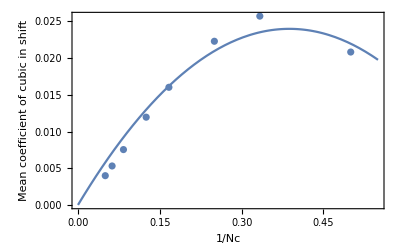

```mathematica
Show[ListPlot[cd,Axes->False,Frame->True,PlotRange->{{0,0.55},Automatic},FrameLabel->{"1/Nc","Mean coefficient of cubic in shift"}],Plot[ffcd,{x,0,.55}]]
```

Plot error as a function of shift in some random shift direction

```mathematica
maxData=2Pi;data=Block[{rd=randomDirection[]},Table[Block[{shift=x If[False,IdentityMatrix[nc^2-1][[1]],rd],sg},sg=shift.suGenerators[nc];{Norm[shift,2],Norm[IdentityMatrix[nc]+I sg-sg.sg/2!-MatrixExp[I sg],2]}],{x,0,maxData, maxData/20}]];
```

```mathematica
ff=Fit[data,{x^3,x^4,x^5},x]
```

0.0267015 x^3-0.000323406 x^4-0.000089854 x^5

```mathematica
Apply[List,ff]/.x->maxData
```

{6.6233,-0.504043,-0.879907}

```mathematica
Show[ListPlot[data],Plot[{ff,x^3/48},{x,0,maxData}]]
```

## Identity staple example, SU(3)

Special case where the sum of staples is proportional to the identity matrix.

```mathematica
diagValue=Cos[x1]+Cos[x2]+Cos[-x1-x2]
```

Cos[x1]+Cos[x2]+Cos[x1+x2]

Saddle Points

```mathematica
Solve[{D[diagValue,x1]==0,D[diagValue,x2]==0},{x1,x2}]
```

{{x1→ConditionalExpression[2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[π+2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[-(2 π)/3+2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[-(2 π)/3+2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[(2 π)/3+2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[π+2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[π+2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[π+2 π C[2],C[2]∈ℤ]}}

Hessian

```mathematica
hess=Outer[D[diagValue,#1,#2]&,{x1,x2},{x1,x2}]
```

{{-Cos[x1]-Cos[x1+x2],-Cos[x1+x2]},{-Cos[x1+x2],-Cos[x2]-Cos[x1+x2]}}

```mathematica
dh=Det[hess]
```

Cos[x1] Cos[x2]+Cos[x1] Cos[x1+x2]+Cos[x2] Cos[x1+x2]

```mathematica
Block[{limit=Pi 4/3},Show[Plot3D[diagValue,{x1,-limit,limit},{x2,- limit, limit},RegionFunction->Function[{x1,x2},Block[{x3=-x1-x2},Abs[x1-x2]<2 Pi&&Abs[x1-x3]<2Pi&&Abs[x2-x3]<2 Pi]]],Graphics3D[{PointSize[0.02],Table[Point[{x1,x2,diagValue}],{x1,-4/3 Pi,2 Pi,2 Pi},{x2,-4/3 Pi,2 Pi,2 Pi}],Table[Point[{x1,x2,diagValue}],{x1,-2/3 Pi,2 Pi,2 Pi},{x2,-2/3 Pi,2 Pi,2 Pi}],Table[Point[{x1,x2,diagValue}],{x1,-Pi,Pi,Pi},{x2,-Pi,Pi,Pi}]}]]]
```

### Test saddle point routine

Run this as a group

```mathematica
sqrtU1=SUPower[u1=randomSUMatrix[3],0.25];
phi1=centerPhases[u1]
```

{0.0697439,2.72834,-2.79808}

```mathematica
{sqrtU2,maxShift}=linkSaddlePointStep[sqrtU1,sqrtU1];maxShift
```

0.0011188

```mathematica
phi2=centerPhases[sqrtU2.sqrtU1]
```

{0.0355178,1.36384,-1.39936}

```mathematica
Block[{limit=3Pi/2},Show[DensityPlot[diagValue,{x1,-limit,limit},{x2,-limit,limit},Epilog->{Thickness[0.02],Line[{Take[phi1,2],Take[phi2,2]}],PointSize[0.02],Table[Point[{y1,y2}],{y1,-4/3 Pi,2 Pi,2 Pi},{y2,-4/3 Pi,2 Pi,2 Pi}],Table[Point[{y1,y2}],{y1,-2/3 Pi,2 Pi,2 Pi},{y2,-2/3 Pi,2 Pi,2 Pi}],Table[Point[{y1,y2}],{y1,-Pi,Pi,Pi},{y2,-Pi,Pi,Pi}]}],DensityPlot[dh,{x1,-limit,limit},{x2,-limit,limit},PlotRange->{-0.1,0.1}]]]
```

## Input gauge configurations

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
<<"../data/3-3/periodic-22-42-1.m"
```

```mathematica
<<"../data/3-3/periodic-22-42-1-cool.m";
```

```mathematica
<<"../data/3-3/periodic-22-42-5.m"
```

```mathematica
<<"../data/3-3/periodic-22-80-5.m"
```

```mathematica
<<"../data/3-4/periodic-16-28-1.m"
```

```mathematica
<<"../data/3-4/periodic-16-33-4.m"
```

```mathematica
<<"../data/3-4/periodic-20-150-5.m"
```

```mathematica
<<"../data/3-3/winding-20-80-0-5.m"
```

```mathematica
<<"../data/3-3/winding-20-80-1-5.m"
```

```mathematica
<<"../data/3-4/winding-20-60-0-4.m"
```

```mathematica
<<"../data/3-4/winding-20-60-1-4.m"
```

```mathematica
<<"../data/3-6/periodic-18-90-1.m"
```

```mathematica
<<"../data/3-6/periodic-18-170-1.m"
```

```mathematica
{nd,nc,beta,latticeDimensions,Dimensions[gaugeField]}
```

{3,3,8.175,{6,6,6},{3,216,3,3}}

Test that links are approximately SU (N)

```mathematica
Length[badMatrices=Select[Flatten[gaugeField,1],Not[SUMatrixQ[#,1.0 10^-10]]&]]
```

0

## Plaquette distribution

The plaquette values, if rescaled to the [0,1] interval, generally fit a Beta distribution, but we can equivalently use a Gamma distribution for small lattice spacings.

```mathematica
useGammaDistribution=True;
```

```mathematica
Histogram[data=Flatten[Table[Table[(1-plaquette[dir1,dir2,latticeCoordinates[i]]/nc)/If[useGammaDistribution,1,2],{i,latticeVolume[]}],{dir1,2},{dir2,dir1+1,nd}]]]
```

```mathematica
{Mean[data],dist=FindDistribution[data,TargetFunctions->Which[useGammaDistribution,{GammaDistribution},True,{BetaDistribution},True,All]]}
```

{0.0650492,GammaDistribution[4.03725,0.0161123]}

Distribution for 1 - Tr(plaquette)/nc

```mathematica
TableForm[dm={{"nd","nc","beta","mean","alpha","beta"},{3,3,42.,0.0650492058072443,4.0372454261752875,0.016112274320900954},{3,3,80.,0.03371067322265413,4.011655372432331,0.008403182749520672},{3,4,28.,0.1923250246554901,7.7282971359028245,0.02488582171194133},{3,4,33.,0.1604205616819077,7.670953223240458,0.02091272844591148},{3,4,150.,0.03380841583718067,7.620434296041462,0.004436547121053944},{3,6,90.,0.13525994258717414,18.387360829900825,0.007356136850654697},{3,6,170.,0.07017369456939337,18.102497926494276,0.0038764647207436133}}]
```

nd | nc | beta | mean | alpha | beta
3 | 3 | 42. | 0.0650492 | 4.03725 | 0.0161123
3 | 3 | 80. | 0.0337107 | 4.01166 | 0.00840318
3 | 4 | 28. | 0.192325 | 7.7283 | 0.0248858
3 | 4 | 33. | 0.160421 | 7.67095 | 0.0209127
3 | 4 | 150. | 0.0338084 | 7.62043 | 0.00443655
3 | 6 | 90. | 0.13526 | 18.3874 | 0.00735614
3 | 6 | 170. | 0.0701737 | 18.1025 | 0.00387646

```mathematica
Fit[Log[Map[#[[{2,3,5}]]&,Rest[dm]]],{1,x,y},{x,y}]
```

-0.957013+2.19225 x-0.0130246 y

```mathematica
alphaf=Fit[Map[#[[{2,3,5}]]&,Rest[dm]],{x,x^2,x^2/y},{x,y}]
```

-0.383726 x+0.567826 x^2+(0.336766 x^2)/y

```mathematica
Fit[Log[Map[#[[{2,3,6}]]&,Rest[dm]]],{1,x,y},{x,y}]
```

-0.276496-0.00344917 x-1.02658 y

```mathematica
betaf=Fit[Map[#[[{2,3,6}]]&,Rest[dm]],{1/y,1/(x y),1/y^2},{x,y}]
```

1.27185/y^2+0.655795/y-0.0190906/(x y)

```mathematica
Series[alphaf betaf,{y,Infinity,2},{x,Infinity,-1}]
```

(0.372377 x^2-0.262486 x+O[1/x]^0)/y+(0.943037 x^2-0.49447 x+O[1/x]^0)/y^2+O[1/y]^3

```mathematica
dist=GammaDistribution[nc^2/2,2/(3 beta)]
```

GammaDistribution[9/2,0.015873]

```mathematica
Mean[GammaDistribution[a1,b1]]
```

a1 b1

```mathematica
TableForm[Map[{#[[2]],#[[3]],#[[4]],#[[2]]^2/(3 #[[3]]),#[[2]]^4/(#[[3]]^2 2 Pi)}&,dm]]
```

nc | beta | mean | nc^2/(3 beta) | nc^4/(2 beta^2 π)
3 | 42. | 0.0650492 | 0.0714286 | 0.00730814
3 | 80. | 0.0337107 | 0.0375 | 0.0020143
4 | 28. | 0.192325 | 0.190476 | 0.051969
4 | 33. | 0.160421 | 0.161616 | 0.0374138
4 | 150. | 0.0338084 | 0.0355556 | 0.00181083
6 | 90. | 0.13526 | 0.133333 | 0.0254648
6 | 170. | 0.0701737 | 0.0705882 | 0.00713719

```mathematica
Block[{width=0.0025},Show[Histogram[data,{width},Axes->False,Frame->True],Plot[Length[data] width PDF[dist][x],{x,0,3 Mean[data]}]]]
```

## Gauge Invariant Shifts

The gauge transforms should leave the action invariant.  Thus any small shift in the direction of a gauge transform should have zero gradient and zero second derivative.

Orthogonalizing the associated matrix creates a matrix that is roughly 50% dense.  This seems to be independent of the basis ordering.  For instance, going to checkerboard (linearSiteIndex[]) just changes the sparsity pattern.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

Create trivial lattice with one non-trivial link.

```mathematica
nd=3;nc=2;latticeDimensions={2,1,1};
If[True,makeTrivialLattice[randomGauge->False];setLink[2,{1,1,1},MatrixExp[I Pi RandomReal[] suGenerators[][[1]]]],gaugeField=Table[If[dir==1,{{0,1},{1,0}},IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}];Clear[linearSiteIndex];
Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}]];averagePlaquette[]
```

0.864238

```mathematica
<<"mma-lib/linear-algebra.m"
```

```mathematica
rl=Chop[makeRootLattice[]];
Dimensions[sh=gaugeTransformShifts[rl]]
```

{1728,5184}

```mathematica
MatrixPlot[sh.Transpose[sh]]
```

Find the condition number of the matrix sh.Transpose[sh]:
get 10.5 for data/3-3/periodic-6-8.175-3.m
get 24 for 3-4/periodic-16-33-4.m

```mathematica
condition[sh.Transpose[sh]]
```

10.5141

Convergence of conjugate gradients for this matrix is this to the number of steps:
get 0.52 for data/3-3/periodic-6-8.175-3.m
and 0.66 for second case

```mathematica
(Sqrt[%]-1)/(Sqrt[%]+1)
```

0.528585

```mathematica
libGaugeField=latticeSaddlePointStep[cutoffValue->Infinity,storePairs->True,fixedDir->-1];
```

cutoff:  ∞

times:  {0.0085,0.01218,0.000864,0.0006}

Transpose[sh].sh is symmetric positive semi - definite.  The null space corresponds to non-gauge shifts.  Note that Transpose[sh].sh is still quite sparse.

```mathematica
Tally[Chop[Sort[Eigenvalues[Transpose[sh].sh]]]]
```

Eigenvalues::arh: Because finding 5184 out of the 5184 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

Test that the gradients are orthogonal to all gauge transforms.

```mathematica
Tally[Chop[sh.grad0]]
```

{{0,6}}

However, sine the Hessian is quadratic in the shifts, it is not necessarily in the direction of two infinitesimal gauge transforms.

```mathematica
MatrixPlot[Chop[sh.hess0.Transpose[sh]]]
```

Orthonormal basis of gauge transforms.  We see that we get roughly 50% sparsity.

```mathematica
MatrixPlot[sho=Orthogonalize[sh]]
```

Project onto subspace of physical degrees of freedom, this results in a dense matrix.

```mathematica
Dimensions[proj=NullSpace[sh]]
```

{13,18}

Verify orthonormality of the projection.

```mathematica
Tally[Flatten[Chop[proj.Transpose[proj]]],(Abs[#1-#2]<10^-12)&]
```

{{1.,13},{0,156}}

Verify unitarity of the adjoint color matrix for some random element of SU(nc):  
        2 Tr[u.suGenerator[a].ConjugateTranspose[u].suGenerator[b]].  
Also, this matrix should be real-valued.  This matrix comes up in the analytic calculations.

```mathematica
Block[{nc=2},ff=Chop[Block[{u=randomSUMatrix[]},Outer[2 Tr[u.#1.ConjugateTranspose[u].#2]&,suGenerators[],suGenerators[],1]]]]
```

{{0.420012,-0.865015,-0.27448},{-0.810949,-0.221975,-0.541376},{0.407371,0.449973,-0.794716}}

```mathematica
Chop[ff.ConjugateTranspose[ff]]
```

{{1.,0,0},{0,1.,0},{0,0,1.}}

## Lattice stationary point

### Trivial lattice

```mathematica
nd=3;nc=5;latticeDimensions={2,2,2};
makeTrivialLattice[randomGauge->True];averagePlaquette[]
```

1.

```mathematica
libGaugeField=latticeSaddlePointStep[storePairs->True,fixedDir->0];
```

cutoff:  1000000

times:  {3.09,3.40822,0.34524,0.00464}

Symmetries of the lattice action.   Gauge fixing removes one dimension worth.  Difference is 9 for SU(2), 24 for SU(3), 45 for SU(4), 72 for SU(5), independent of the size of the lattice.  In general, the difference is 3 (nc^2-1).

Also, all curvatures are negative, indicating that this a a local minimum of the action, since the action is 1-Re(Tr(plaquettte))/Nc.

The result is independent of gauge choice.

```mathematica
{Length[proj0[[1]]],Length[proj0[[1]]]/nd}
```

{576,192}

Zero curvature would indicate a gauge symmetry.

```mathematica
Tally[Rationalize[Chop[pairs0]]]
```

{{{-6,0},48},{{-4,0},144},{{-2,0},144},{{0,0},72}}

### Compare different strategies.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
cutoff=Min[Pi .01^(1/3),Sqrt[1-averagePlaquette[]]]
```

0.634944

Find fraction of shift that is non-gauge transformation.

```mathematica
Dimensions[dynamicShifts=NullSpace[gp=gaugeTransformShifts[makeRootLattice[]]]]
```

{3456,5184}

```mathematica
gaugeFieldAll=latticeSaddlePointStep[storePairs->True,fixedDir->-1];pairsAll=pairs0;ooprojAll=oo0.proj0;
```

applyCutoff3:  282 of 5184 zeros

applyCutoff2: rescale maxNorm 8.84035 to 2.

times:  {8.18,9.774267,22.73788,0.06974}

```mathematica
(Norm[dynamicShifts.#]/Norm[#])&[grad0]
```

1.

On lattices with more than one link in each direction, the diagonal is zero.  But off-diagonal elements are non-zero since the quadratic expansion violates gauge invariance.

```mathematica
Tr[gp.hess0.Transpose[gp]]
```

1.01377×10^-13

```mathematica
gaugeFieldDynamic=latticeSaddlePointStep[storePairs->True,fixedDir->0];pairsDynamic=pairs0;ooprojDynamic=oo0.proj0;
```

applyCutoff3:  133 of 3456 zeros

applyCutoff2: rescale maxNorm 5.15131 to 2.

times:  {8.38,10.06802,32.77853,0.0634}

Map to the shift on the full lattice:

```mathematica
ffdd=2;Dimensions[axialProj=Block[{proj=Association[],i,j},Do[Block[{coords=latticeCoordinates[i]},proj[{coords2grad[ffdd][dir,coords,k],coords2grad[-1][dir,coords,k]}]=1],{dir,nd},{i,latticeVolume[]},{k,nc^2-1}];SparseArray[Normal[proj]]]]
```

{1152,1536}

```mathematica
setAxialGauge[ffdd]
```

```mathematica
gaugeFieldAxial=latticeSaddlePointStep[storePairs->True,fixedDir->ffdd];pairsAxial=pairs0;ooprojAxial=oo0.proj0.axialProj;
```

cutoff:  1

applyCutoff3 zeros: {16,1152}

applyCutoff2 rescale: {13.1624,1}

times:  {2.18,2.51081,0.31219,0.01825}

#### Distribution of shifts

Need to turn on switch in function applyCutoff3 to accumulate data for this plot.

```mathematica
ListPlot[{Map[{#[[1]],Abs[#[[2]]]}&,goodPairs0],Map[{#[[1]],Abs[#[[2]]]}&,badPairs0]},Axes->False,Frame->True]
```

```mathematica
ListPlot[Map[{#[[1]],Abs[#[[2]]]}&,pairsDynamic],Axes->False,Frame->True]
```

```mathematica
Histogram[{Map[First,pairsAll],Map[First,pairsAxial],Map[First,pairsDynamic]}]
```

Note that a Cauchy Distribution is generated by the ratio of two normally distributed variables.

```mathematica
fitt=FindDistribution[Map[#[[2]]/#[[1]]&,pairsDynamic]]
```

CauchyDistribution[-0.00445658,0.301532]

```mathematica
Block[{w=0.2,max=2},Show[Histogram[Map[#[[2]]/#[[1]]&,pairsDynamic],{w},Axes->False,Frame->True,PlotRange->{{-max,max},All}],Plot[PDF[fitt,x]Length[pairsDynamic] w,{x,-max,max},PlotRange->All]]]
```

We see that there is a good fit in the tails and at the peak.

```mathematica
Block[{w=0.2,data=Map[Abs[#[[2]]/#[[1]]]&,pairsDynamic]},Show[Histogram[data,{"Log",{w}},ScalingFunctions->"Log",Axes->False,Frame->True,PlotRange->All],LogPlot[ 2(CDF[fitt,Exp[x] 10^(w/2)]-CDF[fitt,Exp[x]10^(-w/2)])Length[data],{x,Log[Min[data]],Log[Max[data]]},PlotRange->All]]]
```

```mathematica
Histogram[{Map[#[[2]]/#[[1]]&,pairsAll],Map[#[[2]]/#[[1]]&,pairsAxial],Map[#[[2]]/#[[1]]&,pairsDynamic]},{0.1},PlotRange->{{-2,2},Automatic},Axes->False,Frame->True,PlotRange->All]
```

#### Compare shift vectors

```mathematica
cosAngle[a_,b_]:=a.b/(Norm[a] Norm[b])
```

```mathematica
Clear[shifts];makeShifts[type_,pairs_,ooproj_]:=(shifts[type,0,0]=-Map[#[[2]]/#[[1]]&,pairs].ooproj;
shifts[type,1,0]=-Apply[applyCutoff3[##,ooproj,1]&,Transpose[pairs]].ooproj;
shifts[type,0,1]=applyCutoff2[shifts[type,0,0]];
shifts[type,1,1]=applyCutoff2[shifts[type,1,0]];)
```

```mathematica
Print["starting All"];
makeShifts["All",pairsAll,ooprojAll];
Print["starting Dynamic"];makeShifts["Dynamic",pairsDynamic,ooprojDynamic];
Print["starting Axial"];makeShifts["Axial",pairsAxial,ooprojAxial];
```

starting All

applyCutoff3:  70 of 1536 zeros

applyCutoff2: rescale maxNorm 256.13 to 1

applyCutoff2: rescale maxNorm 8.26844 to 1

starting Dynamic

applyCutoff3:  32 of 1024 zeros

applyCutoff2: rescale maxNorm 48.3877 to 1

applyCutoff2: rescale maxNorm 6.31072 to 1

starting Axial

applyCutoff3:  48 of 1152 zeros

applyCutoff2: rescale maxNorm 303.041 to 1

applyCutoff2: rescale maxNorm 6.7566 to 1

```mathematica
typeOuter[type_]:=Block[{sh={shifts[type,0,0],shifts[type,1,0],shifts[type,0,1],shifts[type,1,1]}},TableForm[Outer[cosAngle,sh,sh,1]]]
```

```mathematica
typeOuter["All"]
```

1. | 0.0291846 | 1. | 0.0291846
0.0291846 | 1. | 0.0291846 | 1.
1. | 0.0291846 | 1. | 0.0291846
0.0291846 | 1. | 0.0291846 | 1.

```mathematica
typeOuter["Dynamic"]
```

1. | 0.108593 | 1. | 0.108593
0.108593 | 1. | 0.108593 | 1.
1. | 0.108593 | 1. | 0.108593
0.108593 | 1. | 0.108593 | 1.

```mathematica
typeOuter["Axial"]
```

1. | 0.0255151 | 1. | 0.0255151
0.0255151 | 1. | 0.0255151 | 1.
1. | 0.0255151 | 1. | 0.0255151
0.0255151 | 1. | 0.0255151 | 1.

```mathematica
cosAngle[shifts["All",1,1],shifts["Dynamic",1,1]]
```

0.286411

```mathematica
cosAngle[shifts["Dynamic",1,1],shifts["Axial",1,1]]
```

0.0341957

```mathematica
cosAngle[shifts["All",1,1],shifts["Axial",1,1]]
```

0.086668

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["All",i,j]],{i,0,1},{j,0,1}]]
```

0.396732 | 0.396732
0.582136 | 0.582136

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["Dynamic",i,j]],{i,0,1},{j,0,1}]]
```

1. | 1.
1. | 1.

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["Axial",i,j]],{i,0,1},{j,0,1}]]
```

0.78487 | 0.78487
0.798573 | 0.798573

```mathematica
Tally[Chop[Flatten[dynamicShifts.Transpose[dynamicShifts]-IdentityMatrix[1024]]]]
```

{{0,1048576}}

```mathematica
Histogram[shifts["Dynamic",1,1],{.05}]
```

## Junk

```mathematica
phases=centerPhases[centerSUMatrix[1,3]]
```

{(2 π)/3,(2 π)/3,-(4 π)/3}

```mathematica
N[phases,16]
```

{2.094395102393195,2.094395102393195,-4.188790204786391}

```mathematica
Chop[lineLinks[1,{2,3,4}]]
```

```mathematica
plotAction[1,2,3,{1,1,1},{0,4 nc^2/3}]
```

```mathematica
latticeSaddlePoint[5]
```

```mathematica
stats=latticeSaddlePoint[50]
```

```mathematica
ListLogPlot[Map[#[[{1,3}]]&,stats]]
```

```mathematica
ListLogPlot[Map[{#[[1]],norm/.#[[4]]["BestFitParameters"]}&,stats]]
```

```mathematica
ListLogPlot[Map[{#[[1]],aw/.#[[4]]["BestFitParameters"]}&,stats]]
```

```mathematica
stats=latticeSaddlePoint[14]
```

Save resulting lattice

```mathematica
Save["periodic-3-3-22-42-1-fastcool.m",{nd,nc,beta,latticeDimensions,latticeLayout,gaugeField,linearSiteIndex}]
```